# Plots for QFFF Black Holes course

```mathematica
dir="/Users/mb909/Documents/Academic/QFFF - Black Holes/";
yellowbroken=RGBColor[N[237/255],N[233/255],N[104/255]];
yellow=RGBColor[N[220/255],N[250/255],N[27/255]];
greyblue=RGBColor[N[45/255],N[112/255],N[140/255]];
darkgrey=RGBColor[N[30/255],N[70/255],N[87/255]];
darkblue=RGBColor[N[26/255],N[53/255],N[110/255]];
darkerblue=RGBColor[N[44/255],N[71/255],N[131/255]];
blue=RGBColor[N[66/255],N[106/255],N[181/255]];
orange=RGBColor[N[238/255],N[133/255],N[37/255]];
beamerblue=RGBColor[N[37/255],N[20/255],N[172/255]];
green=RGBColor[N[127/255],N[177/255],N[40/255]];
warmred=RGBColor[N[242/255],N[71/255],N[63/255]];
```

## dR/dt and dR/dτ versus R

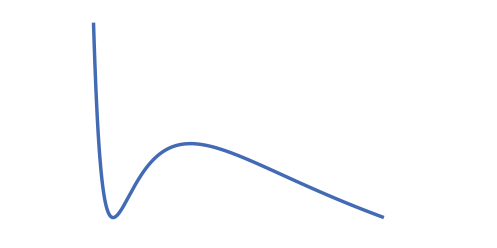

```mathematica
M=1;RMAX=10;ϵ=Sqrt[1-(2M)/RMAX];
Rtplot=Plot[1/ϵ^2(1-(2M)/R)^2((2M)/R-1+ϵ^2),{R,0,RMAX},PlotRange->{{0,RMAX+2},{-0.01,1/4}},AspectRatio->1/2,PlotStyle->Directive[Thickness[0.005],blue](*,AxesLabel->{"R","(Ṙ)^2"}*),Axes->None,AxesStyle->Directive[16,Thickness[0.002]],Ticks->{{{2,""},{10,""}},None}]
```

```mathematica
Export["/Users/mb909/Documents/Academic/QFFF - Black Holes/Rtraw.pdf",Rtplot]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/Rt.pdf

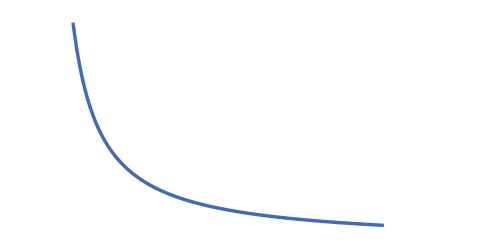

```mathematica
M=1;RMAX=10;ϵ=Sqrt[1-(2M)/RMAX];
Rtauplot=Plot[(2M)/RMAX(RMAX/R-1),{R,0,RMAX},PlotRange->{{0,RMAX+2},Automatic},AspectRatio->1/2,PlotStyle->Directive[Thickness[0.005],blue],(*AxesLabel->{"R","(dR/dτ)^2"},*)Axes->None,AxesStyle->16,Ticks->{{{2,""},{10,""}},None}]
```

```mathematica
Export["/Users/mb909/Documents/Academic/QFFF - Black Holes/Rtauraw.pdf",Rtauplot]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/Rtauraw.pdf

## OEF and IEF plots

```mathematica
rmax=20;
tmax=4;
M=1;
δ=2;
howthick=0.003;
OEFtu[u_,r_]:=u+r+4M Log[Abs[(r-2M)/(2M)]];
OEFtv[v_,r_]:=v-r;
```

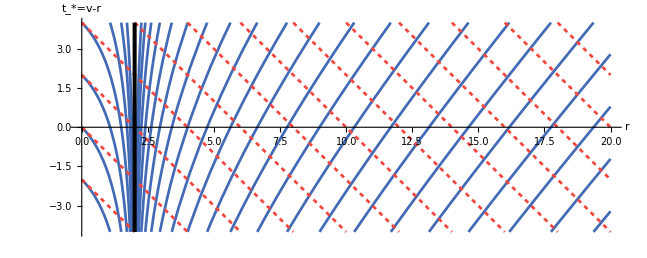

```mathematica
IEFplot=Show[Table[Plot[u+r+4M Log[Abs[(r-2M)/(2M)]],{r,0,rmax},AxesStyle->Arrowheads[0.02],BaseStyle->{FontSize->20,FontFamily-> "Times"},PlotRange->{-tmax,tmax},AspectRatio->2tmax/rmax,PlotStyle->Directive[Thickness[howthick],blue],AxesLabel->{"r","t_*=v-r"}],{u,-50,-32+21δ,δ}]~Join~Table[Plot[v-r,{r,0,rmax},PlotRange->{-tmax,tmax},PlotStyle->{Thickness[howthick],warmred,Dashing[0.005]}],{v,-10,-10+20δ,δ}]~Join~{ParametricPlot[{2M,t},{t,-tmax,tmax},PlotStyle->{Thickness[1.5howthick],Black}]}~Join~{Graphics[Table[Arrow[{{u,2u+4M Log[Abs[(u-2M)/(2M)]]},{u+0.1,2(u+0.1)+4M Log[Abs[((u+0.1)-2M)/(2M)]]}}],{u,20,24}]]}]
```

```mathematica
Export["/Users/mb909/Documents/Academic/QFFF - Black Holes/IEF.eps",IEFplot]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/IEF.eps

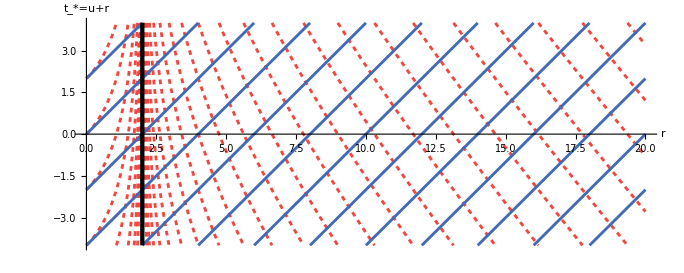

```mathematica
OEFplot=Show[Table[Plot[v-r-4M Log[Abs[(r-2M)/(2M)]],{r,0,rmax},
AxesStyle->Directive[Arrowheads[0.02]],
PlotRange->{-tmax,tmax},AspectRatio->2tmax/rmax,PlotStyle->Directive[Thickness[howthick],warmred,Dashing[0.005]],
Frame->False,
AxesLabel->{"r","t_*=u+r"},
BaseStyle->{FontSize->20,FontFamily-> "Times"}],{v,-12,-14+23δ,δ}]~Join~Table[Plot[u+r,{r,0,rmax},PlotRange->{-tmax,tmax},PlotStyle->{Thickness[howthick],blue}],{u,-40,-40+21δ,δ}]~Join~{ParametricPlot[{2M,t},{t,-tmax,tmax},PlotStyle->{Thickness[1.5howthick],Black}]}]
```

```mathematica
Export["/Users/mb909/Documents/Academic/QFFF - Black Holes/OEF.eps",OEFplot]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/OEF.eps

```mathematica
Solve[(T+X)(T-X)/4==-2,T]
```

{{T→-√(-8+X^2)},{T→√(-8+X^2)}}

## Kruskal Plot

```mathematica
XMAX=5;howthick=0.004;
```

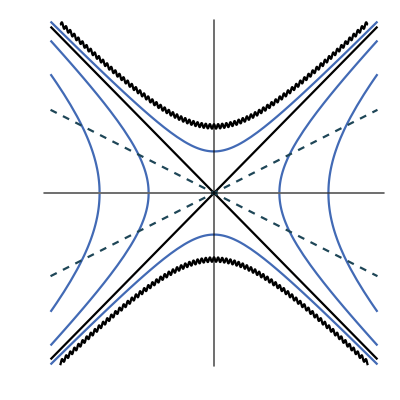

```mathematica
ksplot=Show[{Plot[X,{X,-XMAX,XMAX},AspectRatio->1,Ticks->False,PlotStyle->{Thickness[howthick],Black},AxesStyle->Directive[Arrowheads[0.04],14],LabelStyle-> (FontFamily->"Calibri")(*,AxesLabel->{"X","T"}*)],Plot[-X,{X,-XMAX,XMAX},AspectRatio->1,Ticks->False,AxesStyle->Thin,PlotStyle->{Thickness[howthick],Black}],Plot[√(4+X^2)+ Cos[50X]/15,{X,-XMAX+0.295,XMAX-0.295},AspectRatio->1,Ticks->False,PlotStyle->{Thickness[howthick],Black}],Plot[-√(4+X^2)+ Cos[50X]/15,{X,-XMAX+0.295,XMAX-0.295},AspectRatio->1,Ticks->False,PlotStyle->{Thickness[howthick],Black}]}~Join~Table[Plot[sign √(-UV^2+X^2),{X,-XMAX,XMAX},AspectRatio->1,Ticks->False,AxesStyle->Thin,PlotStyle->Directive[Thickness[howthick],blue]],{UV,2,3.5,1.5},{sign,-1,1,2}]~Join~Table[Plot[sign √(UV^2+X^2),{X,-XMAX,XMAX},AspectRatio->1,Ticks->False,AxesStyle->Thin,PlotStyle->Directive[Thickness[howthick],blue]],{UV,1.25,1.25},{sign,-1,1,2}]~Join~Table[Plot[a X,{X,-XMAX,XMAX},PlotStyle->Directive[Thickness[howthick],darkgrey,Dashed]],{a,-0.5,0.5,1}]]
```

```mathematica
Export["/Users/mb909/Documents/Academic/QFFF - Black Holes/ks.pdf",ksplot]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/ks.pdf

## M^2 in tilde coordinates

```mathematica
T[X_,t_]:=If[t>0,ArcTan[-(Cot[X]^2+1)/(2t)+√(((Cot[X]^2+1)/(2t))^2+Cot[X]^2)],ArcTan[-(Cot[X]^2+1)/(2t)-√(((Cot[X]^2+1)/(2t))^2+Cot[X]^2)]]
AB={{-π/2,-π/2},{π/2,π/2}};
CD={{π/2,-π/2},{-π/2,π/2}};
```

1.5588

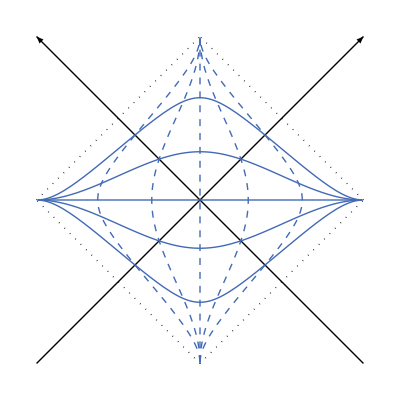

```mathematica
XMAX=π/2-0.012
penrosemink=Show[{Graphics[{Thick,Arrow[AB],Arrow[CD],Dotted,Line[AB/2+{{π/4,-π/4},{π/4,-π/4}}],,Line[AB/2+{{-π/4,π/4},{-π/4,π/4}}],Line[CD/2+{{π/4,π/4},{π/4,π/4}}],Line[CD/2+{{-π/4,-π/4},{-π/4,-π/4}}]}]}~Join~{Plot[0,{X,-XMAX,XMAX},PlotRange->{-π/2,π/2},AspectRatio->1,AxesOrigin->{0,0},Axes->False,PlotStyle->Directive[Thick,blue]],ParametricPlot[{0,X},{X,-XMAX,XMAX},PlotStyle->Directive[Thick,blue,Dashed]]}~Join~Table[Plot[T[X,t],{X,-XMAX,XMAX},PlotStyle->Directive[Thick,blue]],{t,{-1.5,-0.5,0.5,1.5}}]~Join~Table[ParametricPlot[{T[X,t],X},{X,-XMAX,XMAX},PlotRange->{-π/2,π/2},PlotStyle->Directive[Thick,blue,Dashed]],{t,{-1.5,-0.5,0.5,1.5}}]]
```

```mathematica
Export["/Users/mb909/Documents/Academic/QFFF - Black Holes/penroseminkraw.pdf",penrosemink]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/penroseminkraw.pdf

## Penrose diagram of M^2

```mathematica
T[X_,t_]:=If[t>0,ArcTan[-(Cot[X]^2+1)/(2t)+√(((Cot[X]^2+1)/(2t))^2+Cot[X]^2)],ArcTan[-(Cot[X]^2+1)/(2t)-√(((Cot[X]^2+1)/(2t))^2+Cot[X]^2)]]
AB={{-π/2,-π/2},{π/2,π/2}};
CD={{π/2,-π/2},{-π/2,π/2}};
```

1.5588

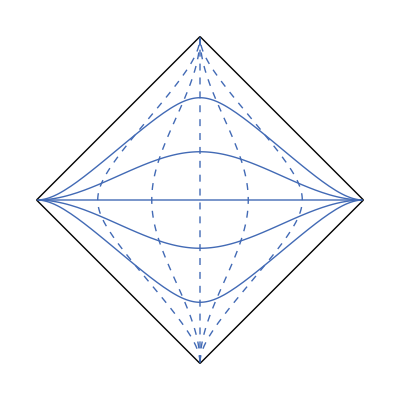

```mathematica
XMAX=π/2-0.012
penroseminkjustlines=Show[{Graphics[{Thick,Line[AB/2+{{π/4,-π/4},{π/4,-π/4}}],Line[AB/2+{{-π/4,π/4},{-π/4,π/4}}],Line[CD/2+{{π/4,π/4},{π/4,π/4}}],Line[CD/2+{{-π/4,-π/4},{-π/4,-π/4}}]}]}~Join~{Plot[0,{X,-XMAX,XMAX},PlotRange->{-π/2,π/2},AspectRatio->1,AxesOrigin->{0,0},Axes->False,PlotStyle->Directive[Thick,blue]],ParametricPlot[{0,X},{X,-XMAX,XMAX},PlotStyle->Directive[Thick,blue,Dashed]]}~Join~Table[Plot[T[X,t],{X,-XMAX,XMAX},PlotStyle->Directive[Thick,blue]],{t,{-1.5,-0.5,0.5,1.5}}]~Join~Table[ParametricPlot[{T[X,t],X},{X,-XMAX,XMAX},PlotRange->{-π/2,π/2},PlotStyle->Directive[Thick,blue,Dashed]],{t,{-1.5,-0.5,0.5,1.5}}]]
```

```mathematica
Export["/Users/mb909/Documents/Academic/QFFF - Black Holes/penroseminkjustlines.pdf",penroseminkjustlines]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/penroseminkjustlines.pdf

## Penrose diagram of M^4

```mathematica
;
```

1.5588

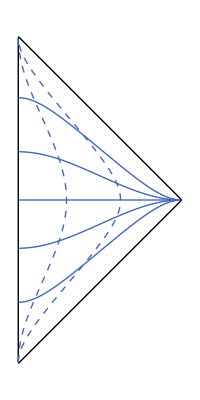

```mathematica
XMAX=π/2-0.012
penrosem4=Show[{Graphics[{Thick,Line[AB/2+{{π/4,-π/4},{π/4,-π/4}}],Line[CD/2+{{π/4,π/4},{π/4,π/4}}]}]}~Join~{Plot[0,{X,0,XMAX},PlotRange->{0,π/2},AspectRatio->1,AxesOrigin->{0,0},Axes->False,PlotStyle->Directive[Thick,blue]],ParametricPlot[{0,X},{X,-XMAX,XMAX},PlotStyle->Directive[Thick,Black]]}~Join~Table[Plot[T[X,t],{X,0,XMAX},PlotStyle->Directive[Thick,blue]],{t,{-1.5,-0.5,0.5,1.5}}]~Join~Table[ParametricPlot[{T[X,t],X},{X,-XMAX,XMAX},PlotRange->{-π/2,π/2},PlotStyle->Directive[Thick,blue,Dashed]],{t,{0.5,1.5}}]]
```

```mathematica
Export["/Users/mb909/Documents/Academic/QFFF - Black Holes/cpmink4draw.pdf",penrosem4]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpmink4draw.pdf

## Penrose Diagram Evaporating Black Hole

```mathematica
~Join~{Plot[5+ Cos[100X]/20,{X,0,1},AspectRatio->1,Ticks->False,PlotStyle->{Thickness[0.02],Black}]}
```

```mathematica
XMAX=5;howthick=0.006;
```

```mathematica
f[x_]:=BezierFunction[{{0,0},{1.25,3},{0,4}}][x]
```

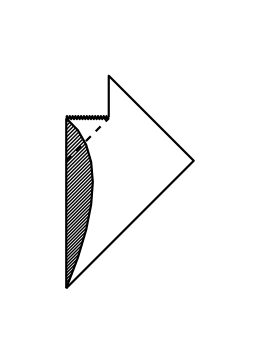

```mathematica
cpevapplot=Show[{Graphics[{Directive[Thickness[howthick]],Line[{{0,0},{0,4}}],Line[{{1,4.03},{1,5},{3,3},{0,0}}],BezierCurve[{{0,0},{1.25,3},{0,4}}]}]}~Join~{Plot[4.015+ Sin[(300/π-1)(X)]/25,{X,0.00,1},AspectRatio->1,Ticks->False,PlotStyle->{Thickness[howthick-0.001],Black}]}~Join~{Graphics[Table[Line[{{0,f[x][[2]]-f[x][[1]]},f[x]}],{x,0,0.99,0.02}]]}~Join~{Plot[x+3,{x,0,1},PlotStyle->{Dashed,Black,Thickness[howthick]}]}~Join~{Graphics[{Directive[White],Line[{{-1,-1},{-1,6},{4,6},{4,-1}}]}]},ImageSize->260]
```

```mathematica
Export[dir~StringJoin~"cpevap.jpg",cpevapplot]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpevap.jpg

## Penrose Diagram Collapsing Black Hole

```mathematica
XMAX=5;howthick=0.01;
```

```mathematica
f[x_]:=BezierFunction[{{0,0},{1.25,3},{0.5,4}}][x]
```

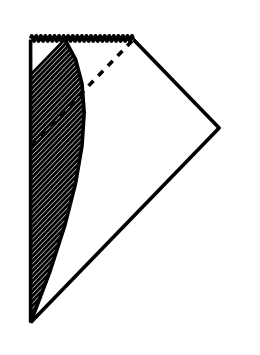

```mathematica
cpcollapse=Show[{Plot[4.015+ Sin[(300/π-1)(X)]/25,{X,0.00,1.5},AspectRatio->4.1/3,Ticks->False,PlotRange->{{-0.1,3},{0,4.1}},PlotStyle->{Thickness[howthick-0.001],Black},Axes->None]}~Join~{Graphics[{Thickness[0.008]}~Join~Table[Line[{{0,f[x][[2]]-f[x][[1]]},f[x]}],{x,0,1.0,0.02}]]}~Join~{Plot[x+2.5,{x,0,1.5},PlotStyle->{Dashed,Black,Thickness[howthick]},PlotRange->{{-0.1,3},{0,4}}]}~Join~{Graphics[{Directive[Thickness[howthick]],Line[{{0,0},{0,4}}],Line[{{1.5,4},{2.75,2.75},{0,0}}],BezierCurve[{{0,0},{1.25,3},{0.5,4}}]}]},ImageSize->260]
```

```mathematica
Export[dir~StringJoin~"cpcollapseraw.pdf",cpcollapse]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpcollapseraw.pdf

## Penrose Diagram Collapsing Black Hole No Interior

```mathematica
XMAX=5;howthick=0.01;
```

```mathematica
f[x_]:=BezierFunction[{{0,0},{1.25,3},{0.5,4}}][x]
```

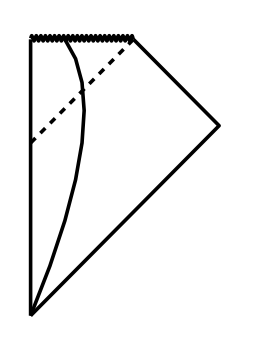

```mathematica
cpcollapse=Show[{Plot[4.015+ Sin[(300/π-1)(X)]/25,{X,0.00,1.5},AspectRatio->4.1/3,Ticks->False,PlotRange->{{-0.1,3},{-0.1,4.1}},PlotStyle->{Thickness[howthick-0.001],Black},Axes->None]}~Join~{Plot[x+2.5,{x,0,1.5},PlotStyle->{Dashed,Black,Thickness[howthick]},PlotRange->{{-0.1,3},{0,4}}]}~Join~{Graphics[{Directive[Thickness[howthick]],Line[{{0,0},{0,4}}],Line[{{1.5,4},{2.75,2.75},{0,0}}],BezierCurve[{{0,0},{1.25,3},{0.5,4}}]}]},ImageSize->260]
```

```mathematica
Export[dir~StringJoin~"cpcollapseraw.pdf",cpcollapse]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpcollapseraw.pdf

## Rindler Space

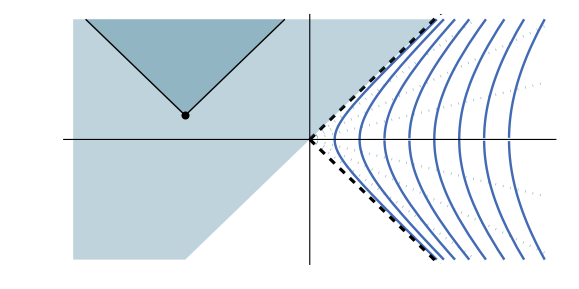

```mathematica
accelerated=Show[Table[Plot[s If[x>0,Sqrt[x^2-b^2]],{x,-9.5,9.5},Ticks->None,AxesStyle->Arrowheads[0.02],PlotRange->{-5,5},AspectRatio->1/2,Ticks->{Range[-10,10],Range[-5,5]},PlotStyle->Directive[Thickness[0.003],blue]],{b,1,8,1},{s,{-1,1}}]~Join~Table[Plot[c x,{x,0,9.5},PlotRange->{-5,5},AspectRatio->1/2,Ticks->{Range[-10,10],Range[-5,5]},PlotStyle->Directive[Thickness[0.003],Dotted,greyblue,Opacity[0.5]]],{c,{-0.75,-0.5,-0.25,0.25,0.5,0.75}}]~Join~Table[Plot[s x,{x,0,9.5},PlotStyle->Directive[Black,Thickness[0.004],Dashed]],{s,{-1,1}}]~Join~{Graphics[{Directive[Opacity[0.3],greyblue],Polygon[{{-9.5,-5},{-9.5,5},{5,5},{-5,-5}}]}]}~Join~{Graphics[{Directive[Opacity[0.3],greyblue],Polygon[{{-5,1},{-9,5},{-1,5}}],Directive[Black,Opacity[1]],PointSize[0.01],Line[{{-9,5},{-5,1},{-1,5}}],Point[{-5,1}]}]}]
```

```mathematica
3
```

```mathematica
Export[dir~StringJoin~"accelerated2.pdf",accelerated]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/accelerated2.pdf

## ESU

```mathematica
R=2
```

2

```mathematica
Show[ParametricPlot3D[{R Cos[u],R Sin[u],z},{u,0,2Pi},{z,-4,4},Mesh->None,PlotStyle->Directive[White,Opacity[0.3]],(*PlotStyle->None,*)Axes->None,Boxed->False,MaxRecursion->10,ViewPoint->{15Cos[-60Degree],12Sin[-60Degree],2}],ParametricPlot3D[{R Cos[u],R Sin[u],z},{u,0,2Pi},{z,-1.5,1.5},PlotStyle->Directive[Opacity[0.7]],Mesh->None],ParametricPlot3D[{R Cos[θ],R Sin[θ],1.5},{θ,0,2Pi},PlotStyle->Directive[Thickness[0.007]]],ParametricPlot3D[{R Cos[θ],R Sin[θ],-1.5},{θ,0,2Pi},PlotStyle->Directive[Thickness[0.007]]](*ParametricPlot3D[{-1.97,0,t},{t,-1.5,1.5},PlotStyle->Directive[Thickness[0.008],Dotted]],ParametricPlot3D[{2.01,0,t},{t,-1.5,1.5},PlotStyle->Directive[Thickness[0.008],Dotted]]*)]
```

-Graphics3D-

```mathematica
Export[dir~StringJoin~"esuds.pdf",%,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/esuds.pdf

```mathematica
plotesumink=Show[ParametricPlot3D[{R Cos[u],R Sin[u],z},{u,0,2Pi},{z,-4.5,4.5},Mesh->None,PlotStyle->Directive[White,Opacity[0.3]],(*PlotStyle->None,*)Axes->None,Boxed->False,MaxRecursion->10,ViewPoint->{10Cos[-60Degree],12Sin[-60Degree],2}],ParametricPlot3D[{R Cos[θ],R Sin[θ],z},{θ,0,2π},{z,Abs[θ-π]-π,-Abs[θ-π]+π},PlotStyle->Directive[Opacity[0.7]],Mesh->None,BoundaryStyle->Directive[Black,Thickness[0.007]]],ParametricPlot3D[{-1.97,0,t},{t,-π,π},PlotStyle->Directive[Thickness[0.008],Dashed]],ParametricPlot3D[{R Cos[θ+π/3],-R Sin[θ+π/3],θ-π/3},{θ,0,Pi},PlotStyle->Directive[Thickness[0.007]]]]
```

-Graphics3D-

```mathematica
Export[dir~StringJoin~"esumink.pdf",%,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/esumink.pdf

/Users/mb909/Documents/Academic/QFFF - Black Holes/esumink.pdf

/Users/mb909/Documents/Academic/QFFF - Black Holes/esumink.pdf

/Users/mb909/Documents/Academic/QFFF - Black Holes/wormhole.pdf

figure.pdf

figure.pdf

-Graphics3D-

## Einstein Rosen bridge

```mathematica
wormhole=ParametricPlot3D[If[ρ>0,{(2M+ρ) Cos[θ],(2M+ρ) Sin[θ],Sqrt[8M ρ]},{(2M-ρ) Cos[θ],(2M-ρ) Sin[θ],-Sqrt[-8M ρ]}],{ρ,-20M,20M},{θ,0,2π},Mesh->Automatic,PlotStyle->(*Directive[Opacity[0.7],White,Specularity[White,20]]*)None,Axes->None,MeshStyle->Directive[Thickness[0.003],Black],Boxed->False,BoundaryStyle->None,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
Export[dir~StringJoin~"wormholeraw.pdf",wormhole]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/wormhole.pdf

## Penrose Diagram for 1+1 Rindler space

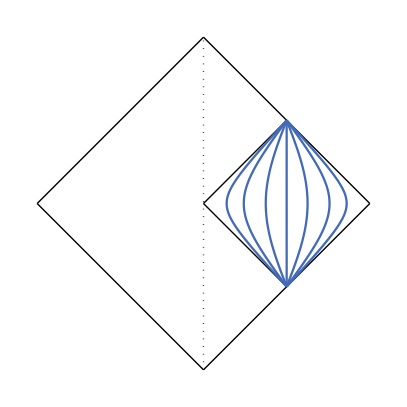

```mathematica
ξ=.
AB={{-π/2,-π/2},{π/2,π/2}};
CD={{π/2,-π/2},{-π/2,π/2}};
XMAX=π/2-0.012;
sol=FullSimplify@Solve[Tan[x+t]Tan[x-t]==ξ^2,x];
penroserindler=Show[{Graphics[{Thick,Line[AB/2+{{π/4,-π/4},{π/4,-π/4}}],Line[AB/2+{{-π/4,π/4},{-π/4,π/4}}],Line[CD/2+{{π/4,π/4},{π/4,π/4}}],Line[CD/2+{{-π/4,-π/4},{-π/4,-π/4}}],Line[{{0,0},{π/4,π/4}}],Line[{{0,0},{π/4,-π/4}}],Dotted,Line[{{0,-π/2},{0,π/2}}]}]}~Join~Table[
ParametricPlot[{(x-π/2)/.{sol[[2,1]]}/.{ξ->n},t},{t,-π/4,π/4},PlotStyle->Directive[Thickness[0.004],blue]],{n,{1/4.5,1/2.5,1/1.5,1,1.5,2.5,4.5}}]]
```

```mathematica
Export[dir~StringJoin~"penroserindlerraw.pdf",penroserindler]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/penroserindlerraw.pdf

## Penrose diagram for Kruskal space

```mathematica
howthick=0.005;
width=0.03;
tmax=1;
height=2
```

2

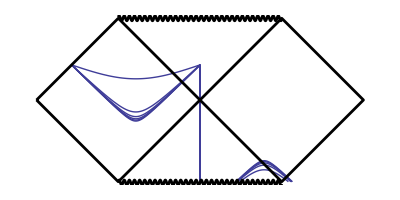

```mathematica
cpkruskal=Show[Table[Plot[If[X<0,(T+3)/.{sol[[1]]},-(T+2)/.{sol[[1]]}],{X,-π/2,π/2},AxesOrigin->{0,0},PlotRange->{{-2,2},{0,2}},AspectRatio->1/2,Axes->None],{c,-2,-102,-20}]~Join~{ParametricPlot[{t,-0.01+width Sin[100t]},{t,-tmax,tmax},PlotRange->{{-2width-2,2+2width},{-2width,2+2width}},Axes->None,Ticks->False,PlotStyle->{Thickness[howthick],Black},AspectRatio->1/2],ParametricPlot[{t,2.0+width Sin[100t]},{t,-tmax,tmax},PlotRange->{{-2width-tmax,tmax+2width},{-2width,2+2width}},Axes->None,Ticks->False,PlotStyle->{Thickness[howthick],Black}]}~Join~{Graphics[{Thickness[howthick],Line[{{-2,1},{-1,2},{0,1},{1,2},{2,1},{1,0},{0,1},{-1,0},{-2,1}}]}]}]
```

```mathematica
Export[dir~StringJoin~"cpkruskal.pdf",cpkruskal]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpkruskal.pdf

## Penrose diagram for sub-extremal RN BH

```mathematica
howthick=0.005;howthicksing=0.004;
width=0.03;
tmax=1;
height=2
```

2

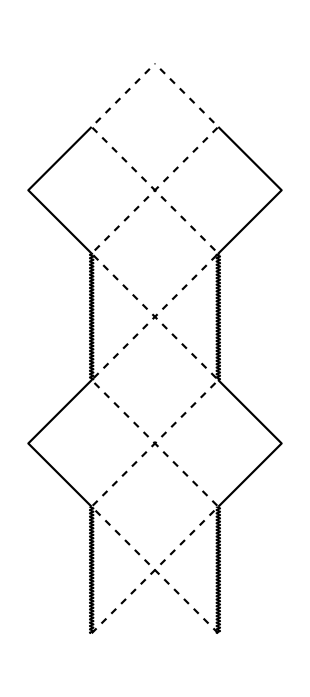

```mathematica
cprnsub=Show[{Graphics[{Thickness[howthick],Line[{{-1,0},{-2,1},{-1,2}}],Line[{{1,2},{2,1},{1,0}}],Line[{{-1,4},{-2,5},{-1,6}}],Line[{{1,6},{2,5},{1,4}}],Dashed,Line[{{1,-2},{-1,0},{0,1},{-1,2},{1,4},{-1,6},{0,7}}],Line[{{-1,-2},{1,0},{0,1},{1,2},{-1,4},{1,6},{0,7}}]}],ParametricPlot[{1-width Cos[120t],t},{t,2,4},PlotStyle->{Thickness[howthicksing],Black}],ParametricPlot[{-1-width Cos[120t],t},{t,2,4},PlotStyle->{Thickness[howthicksing],Black}],ParametricPlot[{1-width Cos[120t],t},{t,0,-2},PlotStyle->{Thickness[howthicksing],Black}],ParametricPlot[{-1-width Cos[120t],t},{t,0,-2},PlotStyle->{Thickness[howthicksing],Black}]}]
```

```mathematica
Export[dir~StringJoin~"cprnsubraw.pdf",cprnsub]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cprnsubraw.pdf

## Penrose diagram for sub-extremal Kerr BH

```mathematica
howthick=0.006;howthicksing=0.004;
width=0.03;
tmax=1;
height=2;
ω=80;
δ=0.15;
```

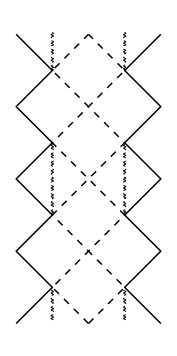

```mathematica
cpsubkerr=Show[{Graphics[{Thickness[howthick],Line[{{-2,-1},{-1,0},{-2,1},{-1,2},{-2,3},{-1,4}}],Line[{{1,4},{2,3},{1,2},{2,1},{1,0},{2,-1}}],Line[{{-1,4},{-2,5},{-1,6},{-2,7}}],Line[{{2,7},{1,6},{2,5},{1,4}}],Dashed,Line[{{0,-1},{-1,0},{0,1},{-1,2},{1,4},{-1,6},{0,7}}],Line[{{0,-1},{1,0},{0,1},{1,2},{-1,4},{1,6},{0,7}}]}]}~Join~Table[ParametricPlot[{1-width Cos[ω t],t},{t,2+s,2+s+δ},PlotStyle->{Thickness[howthicksing],Black}],{s,0,2-δ,1.5δ}]~Join~Table[ParametricPlot[{1-width Cos[ω t],t},{t,-0.9+s,-0.9+s+δ},PlotStyle->{Thickness[howthicksing],Black}],{s,0,1-δ,1.5δ}]~Join~Table[ParametricPlot[{-1-width Cos[ω t],t},{t,-0.9+s,-0.9+s+δ},PlotStyle->{Thickness[howthicksing],Black}],{s,0,1-δ,1.5δ}]~Join~Table[ParametricPlot[{-1-width Cos[ω t],t},{t,2+s,2+s+δ},PlotStyle->{Thickness[howthicksing],Black}],{s,0,2-δ,1.5δ}]~Join~Table[ParametricPlot[{1-width Cos[ω t],t},{t,6+s,6+s+δ},PlotStyle->{Thickness[howthicksing],Black}],{s,0,1.1-δ,1.5δ}]~Join~Table[ParametricPlot[{-1-width Cos[ω t],t},{t,6+s,6+s+δ},PlotStyle->{Thickness[howthicksing],Black}],{s,0,1.1-δ,1.5δ}]]
```

```mathematica
Export[dir~StringJoin~"cpsubkerrraw.pdf",cpsubkerr]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpsubkerrraw.pdf

```mathematica
1∈Reals
```

True

```mathematica
δ=0.1;
```

```mathematica
Table[a[i],{i,0,1.8,0.2}]
```

{a[0.],a[0.2],a[0.4],a[0.6],a[0.8],a[1.],a[1.2],a[1.4],a[1.6],a[1.8]}

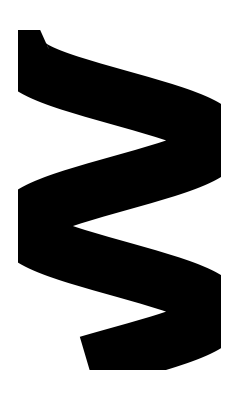
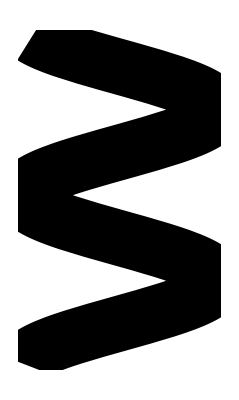
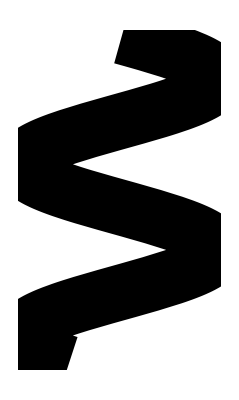
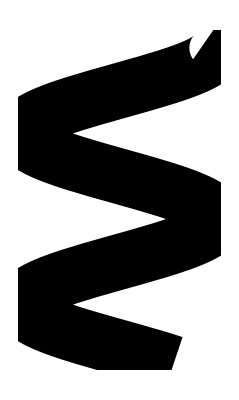
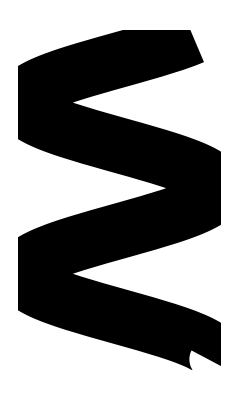
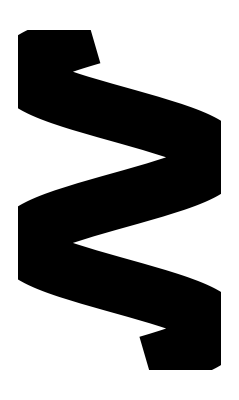
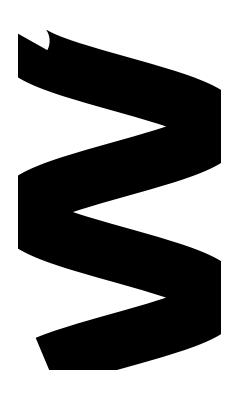
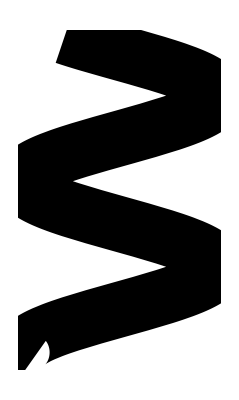

```mathematica
Table[ParametricPlot[{-1-width Cos[120t],t},{t,2+s,2+s+δ},PlotStyle->{Thickness[0.1],Black},Axes->None],{s,0,1.8,0.2}]
```

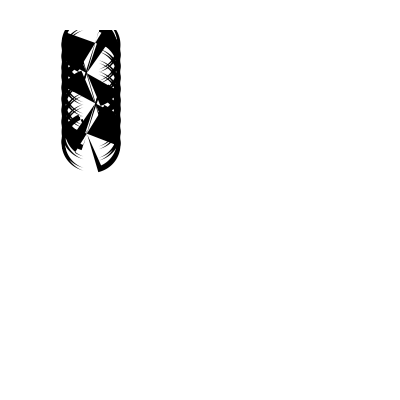
```mathematica
-Graphics-....
```

## Penrose diagram M<0 Schwarzschild

```mathematica
howthick=0.012;
width=0.015;
tmax=2;
```

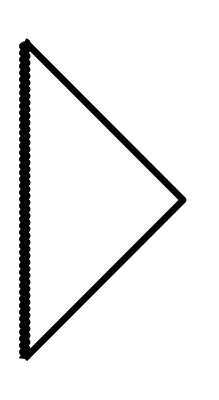

```mathematica
cpnaked=Show[{ParametricPlot[{-width Cos[150t],t},{t,0,tmax},PlotRange->{{-2width,1/2tmax+0.1},{-2width,tmax+2width}},Axes->None,Ticks->False,PlotStyle->{Thickness[howthick],Black}]}~Join~{Graphics[{Thickness[howthick],Line[{{0,0},{1,1},{0,2}}]}]}]
```

```mathematica
Export[dir~StringJoin~"cpnaked.pdf",cpnaked]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpnaked.pdf

```mathematica
Table[ParametricPlot[{1-width Cos[ω t],t},{t,2+s,2+s+δ},PlotStyle->{Thickness[howthicksing],Black}],{s,0,2-δ,1.5δ}]
```

## Penrose diagram Super-Extremal Kerr

```mathematica
howthick=0.006;
width=0.015;
tmax=2;
δ=0.15;
```

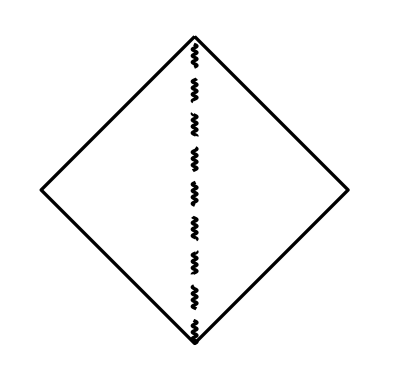

```mathematica
cpkerrsupraw=Show[Table[ParametricPlot[{width Sin[150t],t},{t,s,s+δ},PlotRange->{{-2width-1/2tmax,1/2tmax+0.1},{-2width,tmax+0.01}},Axes->None,Ticks->False,PlotStyle->{Thickness[howthick],Black}],{s,0,tmax-0.2,1.5δ}]~Join~{Graphics[{Thickness[howthick],Line[{{0,2},{-1,1},{0,0},{1,1},{0,2}}]}]}]
```

```mathematica
Export[dir~StringJoin~"cpkerrsupraw.pdf",cpkerrsupraw]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpkerrsupraw.pdf

```mathematica
414.71/12
```

34.5592

```mathematica
650/4//N
```

162.5

## De Sitter hyperboloid

```mathematica
a=1;
```

```mathematica
closed=ParametricPlot3D[{a*Cosh[v]Cos[u],a*Cosh[v]Sin[u],a*Sinh[v]},{v,-2.5,2.5},{u,0,2π},Mesh-> 14,MeshStyle->Directive[Black,Thickness[0.004]],BoundaryStyle->Directive[Thickness[0.004],Black],PlotStyle->None(*Directive[blue,Opacity[0.5],Specularity[White,40]]*),AxesOrigin->{0,0,0},Ticks->None,Boxed->False,AxesStyle->Thickness[0.004]]
```

-Graphics3D-

```mathematica
Export[dir~StringJoin~"desitterhyperboloid.pdf",closed]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/desitterhyperboloid.pdf

## Penrose Diagram de Sitter

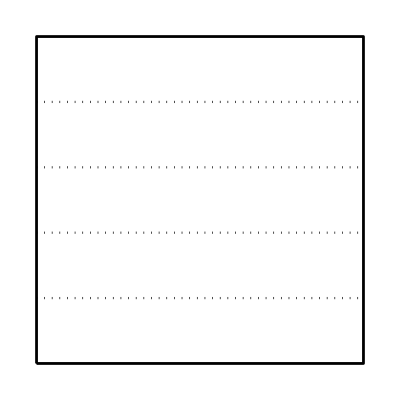

```mathematica
cpdesitter=Show[Graphics[{Thickness[0.005],Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],Thickness[0.004],Dotted,Line[{{0,0.2},{1,0.2}}],Line[{{0,0.4},{1,0.4}}],Line[{{0,0.6},{1,0.6}}],Line[{{0,0.8},{1,0.8}}]}]]
```

```mathematica
Export[dir~StringJoin~"cpdesitterraw.pdf",cpdesitter]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/cpdesitterraw.pdf

## Penrose diagram for extremal RN abridged

```mathematica
XMAX=5;howthick=0.006;
```

```mathematica
f[x_]:=BezierFunction[{{0,0},{1.25,3},{0,4}}][x]
```

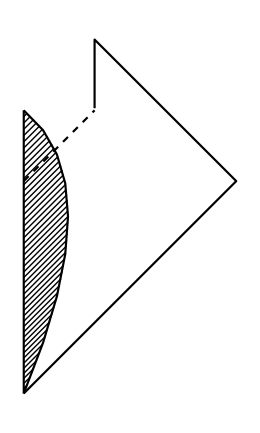

```mathematica
cpevapplot=Show[{Graphics[{Directive[Thickness[howthick]],Line[{{0,0},{0,4}}],Line[{{1,4.03},{1,5},{3,3},{0,0}}],BezierCurve[{{0,0},{1.25,3},{0,4}}]}]}~Join~{Graphics[Table[Line[{{0,f[x][[2]]-f[x][[1]]},f[x]}],{x,0,0.99,0.02}]]}~Join~{Plot[x+3,{x,0,1},PlotStyle->{Dashed,Black,Thickness[howthick]}]},ImageSize->260]
```

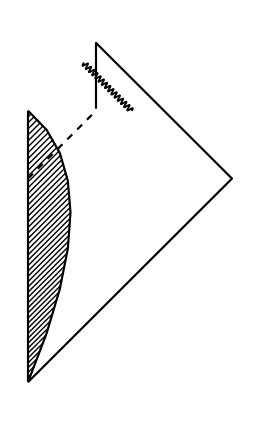

```mathematica
Integrate[1/(a Cosh[t/a]),t]
```

2 ArcTan[Tanh[t/(2 a)]]

```mathematica
2 ArcTan[Tanh[t/(2 a)]]//FullSimplify
```

2 ArcTan[Tanh[t/(2 a)]]

```mathematica
a=1
```

1

```mathematica
t=1
```

1

```mathematica
2 ArcTan[Tanh[t/(2 a)]]//N
```

0.865769

```mathematica
2ArcTan[Exp[t/a]]//N
```

2.43657

```mathematica
ArcTan[1/10]+π/4//N
```

0.885067

```mathematica
ArcTan[10]//N
```

1.47113

```mathematica
ParametricPlot3D[{r Cos[theta],r Sin[theta],Sqrt[8(r-2)]},{r,2,6},{theta,0,2Pi}]
```

-Graphics3D-

```mathematica
Integrate[Exp[-a x^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(√a),Re[a]>0]

## Ring Singularity

```mathematica
ParametricPlot3D[{Cos[θ],Sin[θ],0.01Sin[80θ]},{θ,0,2π},MaxRecursion->15,(*PlotRange->{Automatic,Automatic,{-1,1}},*)Boxed->False,Axes->None,Ticks->None,AxesOrigin->{0,0,0},PlotStyle->Directive[Thickness[0.005],Black]]
```

-Graphics3D-

## Kerr BH

```mathematica
Show[ParametricPlot3D[{Cos[θ],Sin[θ],0},{θ,0,2π},MaxRecursion->15,(*PlotRange->{Automatic,Automatic,{-1,1}},*)Boxed->False,Axes->True,Ticks->None,AxesOrigin->{0,0,0},PlotStyle->Directive[Thickness[0.005],Black]],ParametricPlot3D[{0,Cos[θ],Sin[θ]},{θ,0,2π},PlotStyle->Directive[Thickness[0.005],Black]]]
```

-Graphics3D-

```mathematica
C=.
```

$Failed

```mathematica
x={v,r,θ,χ};
```

```mathematica
Δ=r^2-2M r+a^2;Σ=r^2+a^2 Cos[θ]^2;
```

```mathematica
g={{-(Δ-a^2 Sin[θ]^2)/Σ,1,0,-(a Sin[θ]^2)/Σ(r^2+a^2-Δ)},{1,0,0,-a Sin[θ]^2},{0,0,Σ,0},{-(a Sin[θ]^2)/Σ(r^2+a^2-Δ),-a Sin[θ]^2,0,((r^2+a^2)^2-Δ a^2 Sin[θ]^2)/Σ Sin[θ]^2}};
```

```mathematica
ginv=Inverse[g]//FullSimplify
```

{{(2 a^2 Sin[θ]^2)/(a^2+2 r^2+a^2 Cos[2 θ]),(2 (a^2+r^2))/(a^2+2 r^2+a^2 Cos[2 θ]),0,(2 a)/(a^2+2 r^2+a^2 Cos[2 θ])},{(2 (a^2+r^2))/(a^2+2 r^2+a^2 Cos[2 θ]),(a^2-2 M r+r^2)/(r^2+a^2 Cos[θ]^2),0,(2 a)/(a^2+2 r^2+a^2 Cos[2 θ])},{0,0,1/(r^2+a^2 Cos[θ]^2),0},{(2 a)/(a^2+2 r^2+a^2 Cos[2 θ]),(2 a)/(a^2+2 r^2+a^2 Cos[2 θ]),0,(2 Csc[θ]^2)/(a^2+2 r^2+a^2 Cos[2 θ])}}

```mathematica
n=FullSimplify@Inverse[g].{0,1,0,0}
```

{(2 (a^2+r^2))/(a^2+2 r^2+a^2 Cos[2 θ]),(a^2-2 M r+r^2)/(r^2+a^2 Cos[θ]^2),0,(2 a)/(a^2+2 r^2+a^2 Cos[2 θ])}

```mathematica
nAtOuter=n/.{r->M+Sqrt[M^2-a^2]}//FullSimplify
```

{-(2 M)/(-2 M+(M-√(-a^2+M^2)) Sin[θ]^2),0,0,(2 a)/(4 M (M+√(-a^2+M^2))-2 a^2 Sin[θ]^2)}

```mathematica
nAtOuterNormalised=nAtOuter/nAtOuter[[1]]//FullSimplify
```

{1,0,0,(M-√(-a^2+M^2))/(2 a M)}

```mathematica
ξ=nAtOuterNormalised
```

{1,0,0,(M-√(-a^2+M^2))/(2 a M)}

```mathematica
ginvout=ginv/.{r->M+Sqrt[M^2-a^2]}//FullSimplify
```

{{(2 a^2 Sin[θ]^2)/(4 M (M+√(-a^2+M^2))-2 a^2 Sin[θ]^2),-(2 M)/(-2 M+(M-√(-a^2+M^2)) Sin[θ]^2),0,(2 a)/(4 M (M+√(-a^2+M^2))-2 a^2 Sin[θ]^2)},{-(2 M)/(-2 M+(M-√(-a^2+M^2)) Sin[θ]^2),0,0,(2 a)/(4 M (M+√(-a^2+M^2))-2 a^2 Sin[θ]^2)},{0,0,1/((M+√(-a^2+M^2))^2+a^2 Cos[θ]^2),0},{(2 a)/(4 M (M+√(-a^2+M^2))-2 a^2 Sin[θ]^2),(2 a)/(4 M (M+√(-a^2+M^2))-2 a^2 Sin[θ]^2),0,Csc[θ]^2/(2 M (M+√(-a^2+M^2))-a^2 Sin[θ]^2)}}

```mathematica
ξ.ginv.ξ//FullSimplify
```

(-(a^2+2 M (-M+√(-a^2+M^2))) Csc[θ]^2+4 a^2 M (M-√(-a^2+M^2)+a^2 M Sin[θ]^2))/(2 a^2 M^2 (a^2+2 r^2+a^2 Cos[2 θ]))

```mathematica
ginv//MatrixForm
```

((2 a^2 Sin[θ]^2)/(a^2+2 r^2+a^2 Cos[2 θ]) | (2 (a^2+r^2))/(a^2+2 r^2+a^2 Cos[2 θ]) | 0 | (2 a)/(a^2+2 r^2+a^2 Cos[2 θ])
(2 (a^2+r^2))/(a^2+2 r^2+a^2 Cos[2 θ]) | (a^2-2 M r+r^2)/(r^2+a^2 Cos[θ]^2) | 0 | (2 a)/(a^2+2 r^2+a^2 Cos[2 θ])
0 | 0 | 1/(r^2+a^2 Cos[θ]^2) | 0
(2 a)/(a^2+2 r^2+a^2 Cos[2 θ]) | (2 a)/(a^2+2 r^2+a^2 Cos[2 θ]) | 0 | (2 Csc[θ]^2)/(a^2+2 r^2+a^2 Cos[2 θ]))

```mathematica
ginv[[1,1]]+2ginv[[1,4]](M-√(-a^2+M^2))/(2 a M)+((M-√(-a^2+M^2))/(2 a M))^2 ginv[[4,4]]//FullSimplify
```

(-(a^2+2 M (-M+√(-a^2+M^2))) Csc[θ]^2+4 a^2 M (M-√(-a^2+M^2)+a^2 M Sin[θ]^2))/(2 a^2 M^2 (a^2+2 r^2+a^2 Cos[2 θ]))

```mathematica
Gamma[σ_,ρ_]:=1/2 g[[σ,ρ]]
```

$Failed

```mathematica
k[μ_,ρ_,ν_]:=D[g[[μ,ρ]],x[[ν]]]
```

```mathematica
Gamma[σ_,μ_,ν_]:=Sum[1/2
```

```mathematica
70/5//N
```

14.

```mathematica
48/6//N
```

8.

```mathematica
45*1.42
```

63.9

```mathematica
-108.5+55.5+90.5-10.5-38.5+11.5
```

0.

## Charge Region (under construction)

```mathematica
Show[Plot3D[1Cos[x/2]+ Sin[y/2],{x,-π,π},{y,-π,π},Boxed->False,Axes->None,PlotStyle->Directive[Opacity[0.3],Specularity[White,50]],Mesh->None],ParametricPlot3D[{1Cos[θ],1Sin[θ],Cos[1Cos[θ]/2]+ Sin[1Sin[θ]/2]},{θ,0,2π},PlotStyle->Directive[Thick,Black]]]
```

-Graphics3D-

```mathematica
blue
```

RGBColor[0.258824,0.415686,0.709804]

```mathematica
darkerblue
```

RGBColor[0.172549,0.278431,0.513725]

```mathematica
darkgrey=RGBColor[N[30/255],N[70/255],N[87/255]];
```

```mathematica
colorfn=.
```

```mathematica
height=20;r2=0.5;r1=0.5;colorfn[z_]:= RGBColor[N[(66+z(30-66))/255],N[(106+z(70-106))/255],N[(181-z(87-181))/255]];δ=3;mesh=Automatic;
r[h_]:=((r2-r1)*h/height+r1)(1+0.1Sin[2π h/height])
```

```mathematica
Show[Plot3D[ δ Cos[x/1]+ δ Sin[y/1],{x,-π,π},{y,-π,π},PlotRange->{{-π,π},{-π,π},{-2δ,height+2δ}},Boxed->False,Axes->None,PlotStyle->Directive[Opacity[1],Specularity[White,50]],Mesh->None,BoundaryStyle->None,ViewPoint->{3,1,2}],ParametricPlot3D[{r1 Cos[θ],r1 Sin[θ],0.1+δ Cos[r1 Cos[θ]/1]+ δ Sin[r1 Sin[θ]/1]},{θ,0,2π},PlotStyle->Directive[Thick,Black]],Plot3D[height+δ Cos[x/1]+ δ Sin[y/1],{x,-π,π},{y,-π,π},Boxed->False,Axes->None,PlotStyle->Directive[Opacity[0.6],Specularity[White,50]],Mesh->None,ColorFunction->colorfn,BoundaryStyle->None],ParametricPlot3D[{r2 Cos[θ],r2 Sin[θ],height+δ Cos[r2 Cos[θ]]+ δ Sin[r2 Sin[θ]]},{θ,0,2π},PlotStyle->Directive[Thick,Black]],ParametricPlot3D[{ r[h]Cos[θ],r[h] Sin[θ],h+δ Cos[r[h] Cos[θ]]+δ  Sin[r[h] Sin[θ]]},{θ,0,2π},{h,0,height},PlotStyle->Directive[Opacity[0.3],Specularity[White,50],blue],Mesh->None,ColorFunction->colorfn,BoundaryStyle->None]]
```

-Graphics3D-

```mathematica
Export[dir~StringJoin~"chargeplotraw.pdf",%,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/chargeplotraw.pdf

```mathematica
r[h_]:=(r2-r1)*h/height+r1
```

```mathematica
Plot[-Abs[θ-π]+π,{θ,0,2π}]
```

## Schwarzschild potential

```mathematica
z[r_]:=2 (M+M ProductLog[ⅇ^(-1+r/(2 M))]);j=0;M=1;
```

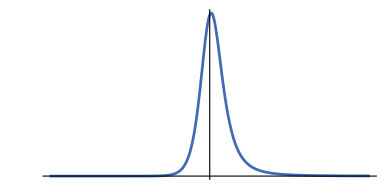

```mathematica
sspot=Plot[(1-(2M)/z[r])((j(j+1))/z[r]^2+(2M)/z[r]^3),{r,-50,50},AspectRatio->1/2,Ticks->None,PlotRange->All,Axes->True,PlotStyle->Directive[Thickness[0.005],blue]]
```

```mathematica
Export[dir~StringJoin~"sspotraw.pdf",sspot]
```

/Users/mb909/Documents/Academic/QFFF - Black Holes/sspotraw.pdf